```mathematica
ClearAll["Global`*"]
```

```mathematica
mesh="/Users/michelecastellana/Documents/finite_elements/generate_mesh/2d/square/solution/vertices.csv";
inputpath="/Users/michelecastellana/Documents/finite_elements/read_write/read_fields/input/";
solutionpath="/Users/michelecastellana/Documents/finite_elements/read_write/read_fields/solution/";
```

```mathematica
L=1;
h=1;
```

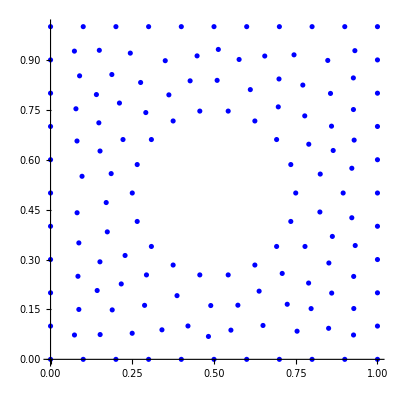

141

```mathematica
tabve=Import[mesh];
tabve=Table[{tabve[[i,1]],tabve[[i,2]]},{i,2,Length[tabve]}];
ListPlot[tabve,PlotStyle->Blue,AspectRatio->1]
Length[tabve]
```

```mathematica
(*write a scalar on csv file by interpolating it on the mesh*)
```

```mathematica
u[x_,y_]:=Cos[2π(x-y)]
```

```mathematica
tabu=Table[{u[x,y]/.{x->tabve[[i,1]],y->tabve[[i,2]]},tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabu,{"f",":0",":1",":2"}]
```

```mathematica
inputpath<>"phi.csv"
```

/Users/michelecastellana/Documents/finite_elements/read_write/read_fields/input/phi.csv

```mathematica
Export[inputpath<>"u.csv",tabu]
```

/Users/michelecastellana/Documents/finite_elements/read_write/read_fields/input/u.csv

```mathematica
plotuexact=Plot3D[u[x,y],{x,0,L},{y,0,h}];
```

```mathematica
t=Import[solutionpath <> "u.csv"];
t=Table[{t[[i,2]],t[[i,3]],t[[i,1]]},{i,2,Length[t]}]
```

```mathematica
δ=Max[Table[Abs[t[[i,3]]-u[t[[i,1]],t[[i,2]]]],{i,1,Length[t]}]]
```

2.5663×10^-15

```mathematica
plotufe=ListPointPlot3D[t,PlotRange->Full,PlotStyle->Red]
```

-Graphics3D-

```mathematica
Show[plotuexact,plotufe]
```

-Graphics3D-